```mathematica
par0[x_]=a*x^2+b*x+c
```

c+b x+a x^2

```mathematica
sh=Solve[par0[0]==h,{a,b,c}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{c→h}}

```mathematica
par1[x_]=par0[x]/.sh[[1]]
```

h+b x+a x^2

```mathematica
stheta=Solve[par1'[0]==Cos[2*theta]/Sin[2*theta],{a,b}]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{b→Cot[2 theta]}}

```mathematica
par2[x_]=par1[x]/.stheta[[1]]
```

h+a x^2+x Cot[2 theta]

```mathematica
szero=Solve[par2'[x]==0,{x}]
```

{{x→-Cot[2 theta]/(2 a)}}

```mathematica
hmax=par2[x/.szero[[1]]]
```

h-Cot[2 theta]^2/(4 a)

```mathematica
g=10;
eh[h_]:=g*h;
ev[v_]:=(v^2)/2;
ve[e_]:=Sqrt[2*e];
heq=(hmax==ev[ve[eh[d-h]]*Cos[2*theta]]/g+h)
```

h-Cot[2 theta]^2/(4 a)==h+(d-h) Cos[2 theta]^2

```mathematica
se=Solve[heq,a]
```

{{a→-Csc[2 theta]^2/(4 (d-h))}}

```mathematica
par[x_]=par2[x]/.se[[1]]
```

h+x Cot[2 theta]-(x^2 Csc[2 theta]^2)/(4 (d-h))

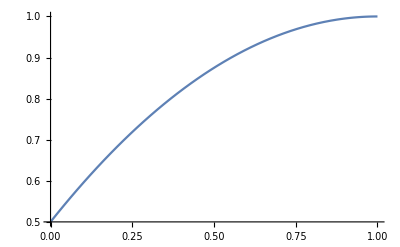

```mathematica
Plot[par[x]/.{d->3/2,h->1/2,theta->Pi/8},{x,0,1}]
```

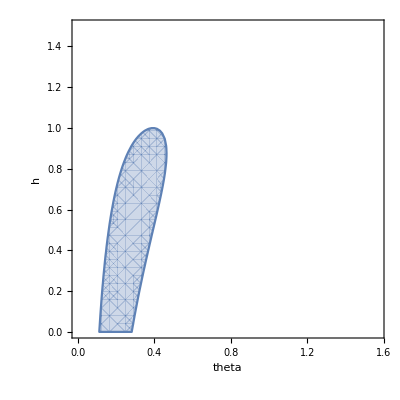

```mathematica
RegionPlot[(par[1]/.{d->3/2})>1,{theta,0,Pi/2},{h,0,3/2},AxesLabel->Automatic]
```

```mathematica
sd=Solve[par[1]==1,d]
```

{{d→(-4 h+4 h^2+4 h Cot[2 theta]+Csc[2 theta]^2)/(4 (-1+h+Cot[2 theta]))}}

```mathematica
dmin=d/.sd[[1]]
```

(-4 h+4 h^2+4 h Cot[2 theta]+Csc[2 theta]^2)/(4 (-1+h+Cot[2 theta]))

```mathematica
Plot3D[If[dmin>h,dmin],{theta,0,Pi/2},{h,0,3/2},PlotRange->Automatic,AxesLabel->Automatic]
```

-Graphics3D-

0

Csc[2 theta]^2/(4 (-1+Cot[2 theta]))

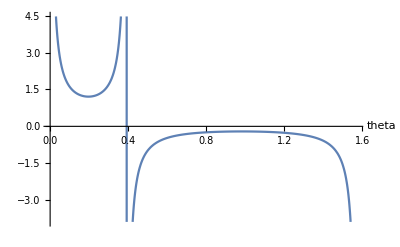

```mathematica
mh=0
dhmin=dmin/.h->mh
Plot[dmin/.h->0,{theta,0,Pi/2},AxesLabel->Automatic]
```

{{theta→1/2 (π-ArcTan[(3 √(2-√2)-(2-√2)^(3/2))/(√(2-√2))])},{theta→1/2 ArcTan[(-3 √(2-√2)+(2-√2)^(3/2))/(√(2-√2))]},{theta→1/2 (-π-ArcTan[(3 √(2+√2)-(2+√2)^(3/2))/(√(2+√2))])},{theta→1/2 ArcTan[(-3 √(2+√2)+(2+√2)^(3/2))/(√(2+√2))]}}

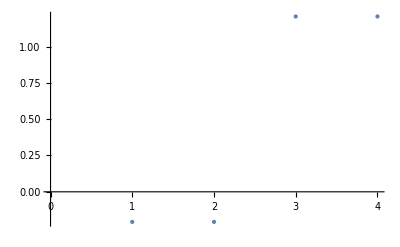

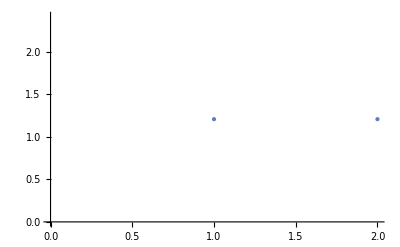

1/2 ArcTan[(-3 √(2+√2)+(2+√2)^(3/2))/(√(2+√2))]

```mathematica
stmin=Solve[D[dhmin,theta]==0]/.C[1]->0
pts=theta/.stmin;
ListPlot[dhmin/.stmin,PlotStyle->{PointSize[Large]}]
pts={pts[[3]],pts[[4]]};
ListPlot[{dhmin/.theta->pts[[1]],dhmin/.theta->pts[[2]]},PlotStyle->{PointSize[Large]}]
mtheta=pts[[2]]
```

```mathematica
md=dhmin/.theta->mtheta
```

((2+√2) (1+((-3 √(2+√2)+(2+√2)^(3/2))^2)/(2+√2)))/(4 (-3 √(2+√2)+(2+√2)^(3/2))^2 (-1+(√(2+√2))/(-3 √(2+√2)+(2+√2)^(3/2))))

Part::partw: Part 4 of {theta→1/2 (π-ArcTan[Power[«2»] Plus[«2»]])} does not exist.

ReplaceAll::reps: {{theta→1/2 (π-ArcTan[«1»])}⟦4⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Csc[2 theta]^2/(4 (-1+Cot[2 theta]))/.{theta→1/2 (π-ArcTan[(3 √(2-√2)-(2-√2)^(3/2))/(√(2-√2))])}⟦4⟧

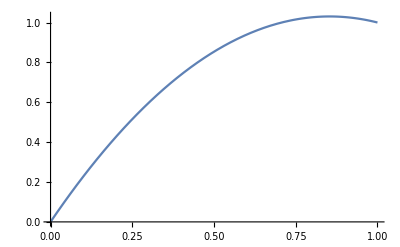

h: 0.

d: 1.20711

theta: 0.19635

```mathematica
(dmin/.h->0)/.stmin[[1]][[4]]
Plot[par[x]/.{h->mh,d->md,theta->mtheta},{x,0,1}]
Print["h: ", N[mh]];
Print["d: ", N[md]];
Print["theta: ", N[mtheta]];
```

```mathematica
pos={0,md};
vel={0,0};
hit=False;
step[dt_]:=Module[
{},
If[
hit&&pos[[1]]>1&&pos[[2]]<0,
pos={0,md};vel={0,0};
hit=False;
];
If[
!hit&&pos[[2]]<mh,
vel={-vel[[2]]*Sin[2*mtheta],-vel[[2]]*Cos[2*mtheta]};
hit=True;
];
pos+=vel*dt;
vel[[2]]-=g*dt;
];
```

```mathematica
cr=0.04;
Animate[
step[dt];
Graphics[{
Black,Thick,Line[{{1,0},{1,1}}],
Red,Thick,Line[0.1*{{Cos[mtheta],-Sin[mtheta]},{-Cos[mtheta],Sin[mtheta]}}],
Thin,Black,Dashed,Circle[{0,md+cr},0.04],
If[hit,Blue,Blue],PointSize[0.04],Point[pos+{0,cr}]
},PlotRange->{{-0.1,3/2+0.1},{-0.1,3/2+0.1}},Frame->True],
{dt,0,0.01,0.0001},
AnimationRunning->False
]
```

```mathematica
pos={0,md};
vel={0,0};
hit=False;
gif=Table[
step[0.005];
Graphics[{
Black,Thick,Line[{{1,0},{1,1}}],
Red,Thick,Line[0.1*{{Cos[mtheta],-Sin[mtheta]},{-Cos[mtheta],Sin[mtheta]}}],
Thin,Black,Dashed,Circle[{0,md+cr},0.04],
If[hit,Blue,Blue],PointSize[0.04],Point[pos+{0,cr}]
},PlotRange->{{-0.1,3/2+0.1},{-0.1,3/2+0.1}},Frame->True],
{280}
];
Export["bounce.gif",gif,"DisplayDurations"->0.04];
```